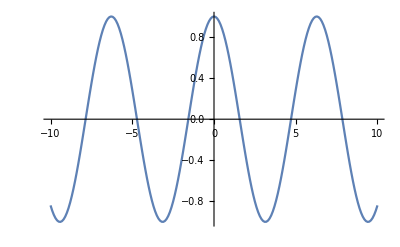

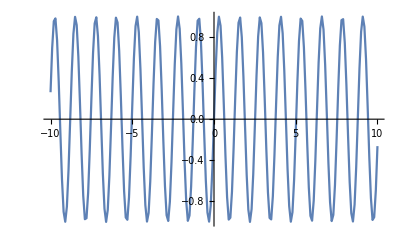

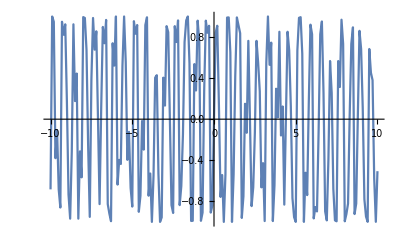

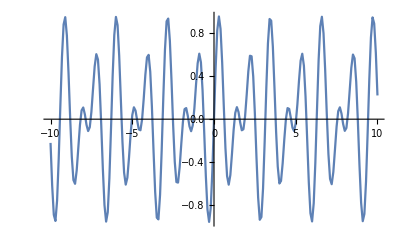

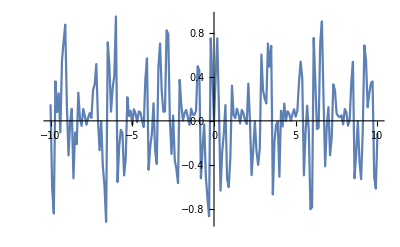

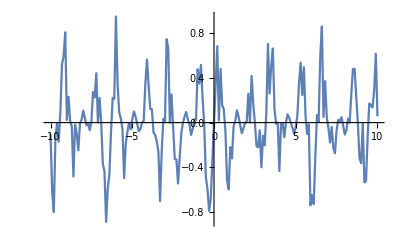

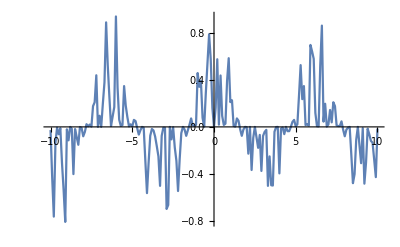

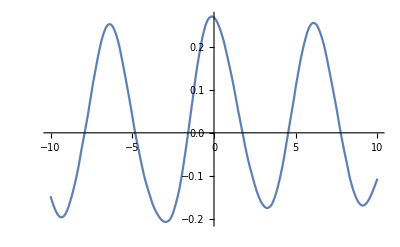

```mathematica
s1[x_]:=Cos[x]
c1[x_]:=Sin[5x]
c2[x_,d_]:=Sin[10x+d*5]
r:=Range[-10,10,.1]
s1p:=Map[s1,r]
c1p:=Map[c1,r]
c2p:=Map[c2,r]
SeedRandom[Round[Pi*Pi]]
list:=List[]
For[i=-10,i<=10,i+=.1,
list=Append[list,c2[i,RandomInteger[]]];
]
ListLinePlot[s1p, DataRange->{-10,10}]
ListLinePlot[c1p, DataRange->{-10,10}]
ListLinePlot[list,DataRange->{-10,10}]
ListLinePlot[s1p*c1p,DataRange->{-10,10}]
ListLinePlot[s1p*c1p*list,DataRange->{-10,10}]
ListLinePlot[s1p*c1p*list*list,DataRange->{-10,10}]
ListLinePlot[s1p*c1p*list*list*c1p,DataRange->{-10,10}]
ListLinePlot[LowpassFilter[s1p*c1p*list*list*c1p,.1],DataRange->{-10,10}]
(*ListLinePlot[s1p*c1p,DataRange->{-10,10}]*)
```

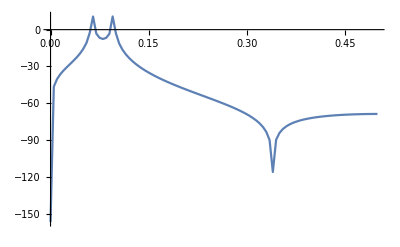

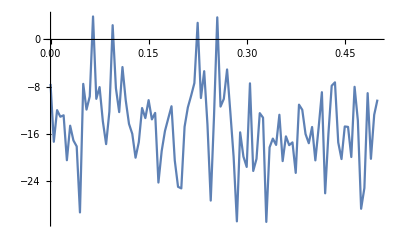

```mathematica
Periodogram[c1p*s1p]
Periodogram[s1p*c1p*list]
```